```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
ρmin=0.;
ρmax=30000.;
c0=1.85*10^6;
fpi=93.5;
cmax=10.^7;
cmin=10.^-2;
rhoend=500.;
```

```mathematica
lT=20;
T=Table[Exp[Log[10^-4]-(Log[10^-4]-Log[100])/lT*(i-1)]//N,{i,1,lT}];
```

```mathematica
V1mub00p01=Flatten[Transpose[Table[Flatten[Import["./mub0_IR0p01/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
slopmub00p01=Table[{SetPrecision[(T[[i]])/124.69765,90],SetPrecision[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1mub00p01]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
V1mub00p05=Flatten[Transpose[Table[Flatten[Import["./mub0_IR0p05/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
slopmub00p05=Table[{SetPrecision[(T[[i]])/124.69765,90],SetPrecision[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1mub00p05]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
V1mub00p1=Flatten[Transpose[Table[Flatten[Import["./mub0_IR0p1/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
slopmub00p1=Table[{SetPrecision[(T[[i]])/124.69765,90],SetPrecision[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1mub00p1]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
V1mub00p3=Flatten[Transpose[Table[Flatten[Import["./mub0_IR0p3/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
slopmub00p3=Table[{SetPrecision[(T[[i]])/124.69765,90],SetPrecision[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1mub00p3]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
V1mub00p5=Flatten[Transpose[Table[Flatten[Import["./mub0_IR0p5/dVd1rdata/dvdr"<>ToString[i]<>".dat"]],{i,1,lT}]]];
slopmub00p5=Table[{SetPrecision[(T[[i]])/124.69765,90],SetPrecision[FindFit[Transpose[{-Log[T/124.69765],Log[1/√V1mub00p5]}][[i-1;;i+1]],a x+b,{a,b},x][[1]][[2]],90]},{i,2,lT-1}];
```

## Plot

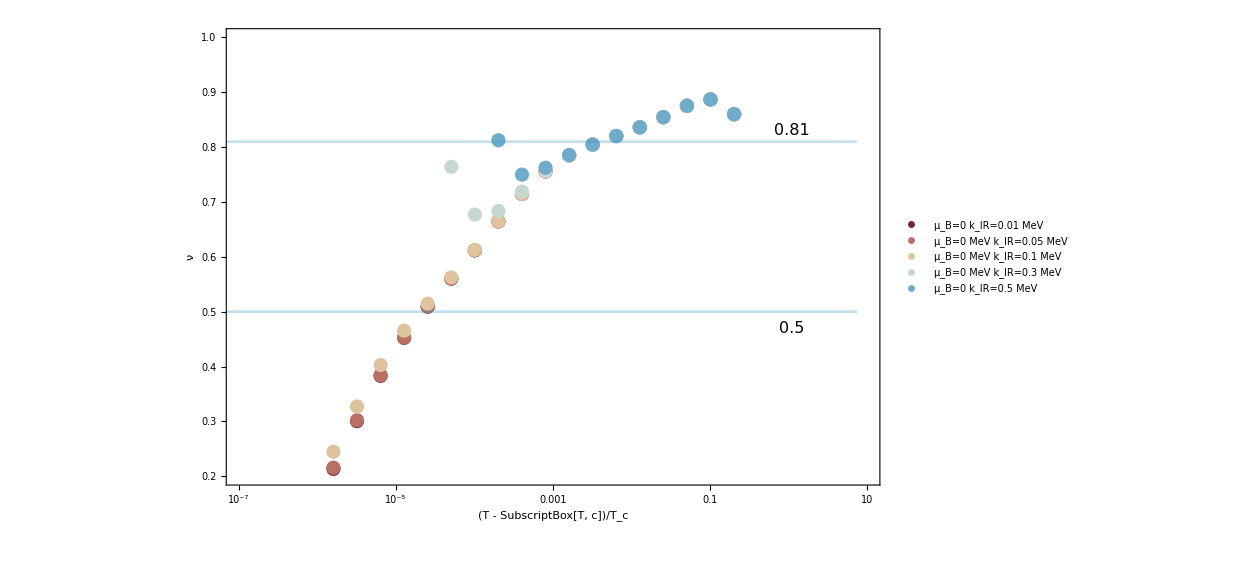

```mathematica
Show[ListPlot[{slopmub00p01,slopmub00p05,slopmub00p1,slopmub00p3,slopmub00p5},ScalingFunctions->{"Log",Automatic},
Frame->True,FrameLabel->{Style["(T - SubscriptBox[T, c])/T_c",25,FontFamily->"Times",Black],Style["ν",25,FontFamily->"Times",Black]},
PlotStyle->Table[Directive[ColorData["RedBlueTones"][i],AbsoluteThickness[3.]],{i,0,1,0.2}],PlotStyle->10,
PlotLegends->Placed[LineLegend[{"μ_B=0 k_IR=0.01 MeV","μ_B=0 MeV k_IR=0.05 MeV","μ_B=0 MeV k_IR=0.1 MeV","μ_B=0 MeV k_IR=0.3 MeV","μ_B=0 k_IR=0.5 MeV"},LabelStyle->16],{0.2,0.6}],
PlotRange->{{10^-7,10},{0.2,1.}},AxesOrigin->{10^-7,0.2},FrameTicksStyle->Directive[15,Black],Epilog->{Text[Style["0.5",16],{0.1,0.47}],Text[Style["0.81",16],{0.1,0.83}]}],ListLinePlot[{{-20,0.5},{2,0.5}},PlotStyle->Opacity[0.3]],ListLinePlot[{{-20,0.81},{2,0.81}},PlotStyle->Opacity[0.3]]]
```